In this analysis, we set everything in terms of the predator body size
Prey body size is then determined as a function of the predator body size: OptPreyMass = f[PredMass]

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqnP = (w*bPred*P*C +(1-w)* bPredSub*Sub*P) - μPred*P/.{bPred->bPred[Mp],bPredSub->bPredSub[Mp],μPred->μPred[Mp]}; (*,σPred->σPred[M],kC->kCons[M],Sub->Sub[M]*)
eqnC = λ*(R/(k/2+R))*C-( σ*(1-R/k)+μ+w*bmort*P)*C/.{k->kRes,λ->λ[Mp],μ->μ[Mp],σ->σ[Mp],bmort->bmort[Mp]};
eqnR = α*R*(1-R/(k))-( λ/Y*(R/(k/2+R)))*C/.{k->kRes,λ->λ[Mp],Y->Y[Mp]};
LVSS = FullSimplify[Solve[{0==eqnP,0==eqnC,0==eqnR},{P,C,R}]];
```

```mathematica
Psol = P/.LVSS[[5]]
Csol = C/.LVSS[[5]]
Rsol = R/.LVSS[[5]]
```

((8 λ[Mp])/w-(8 μ[Mp])/w+((-3 √kRes √w √α √bPred[Mp] √Y[Mp]+√(9 kRes w α bPred[Mp] Y[Mp]-16 λ[Mp] (Sub (-1+w) bPredSub[Mp]+μPred[Mp]))) (kRes w α bPred[Mp] Y[Mp]+2 (Sub (-1+w) bPredSub[Mp]+μPred[Mp]) σ[Mp]))/(√kRes w^(3/2) √α √bPred[Mp] √Y[Mp] (Sub (-1+w) bPredSub[Mp]+μPred[Mp])))/(8 bmort[Mp])

(Sub (-1+w) bPredSub[Mp]+μPred[Mp])/(w bPred[Mp])

kRes/4+(√kRes √(9 kRes w α bPred[Mp] Y[Mp]-16 λ[Mp] (Sub (-1+w) bPredSub[Mp]+μPred[Mp])))/(4 √w √α √bPred[Mp] √Y[Mp])

```mathematica
PsolNoSubsidies= Psol/.w->1
CsolNoSubsidies= Csol/.w->1
```

(8 λ[Mp]-8 μ[Mp]+((-3 √kRes √α √bPred[Mp] √Y[Mp]+√(9 kRes α bPred[Mp] Y[Mp]-16 λ[Mp] μPred[Mp])) (kRes α bPred[Mp] Y[Mp]+2 μPred[Mp] σ[Mp]))/(√kRes √α √bPred[Mp] √Y[Mp] μPred[Mp]))/(8 bmort[Mp])

μPred[Mp]/bPred[Mp]

```mathematica
JacobianFullModel=({
{D[eqnP,P],D[eqnP,C],D[eqnP,R]},
{D[eqnC,P],D[eqnC,C],D[eqnC,R]},
{D[eqnR,P],D[eqnR,C],D[eqnR,R]}})/.{P->Psol,C->Csol,R->Rsol};
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/carnivoredensities_trimmed.csv"}],"csv"];
```

***Declare Metabolic Parameters***

```mathematica
NotebookEvaluate[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/src/metabolic_constants.nb"}]];
```

***Declare Allometric Functions - SPECIFIC TO MODEL AND PERSPECTIVE***

```mathematica
NotebookEvaluate[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/src/allometric_functions_predpersp.nb"}]];
```

***Declare PPMR***

```mathematica
NotebookEvaluate[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/src/ppmr_primary.nb"}]];
```

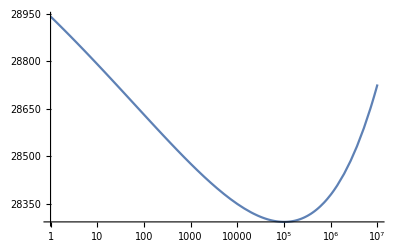

```mathematica
LogLinearPlot[Eprey[M],{M,1,10^7}]
```

```mathematica
(*Sub=Evaluate[NIntegrate[(1/M)*CsolNoSubsidies,{M,10^0,10^7}]];*)(*1*)(*0.1*CsolNoSubsidies;*)
```

```mathematica
(*SubDensity=10*Evaluate[NIntegrate[(1/M)*CsolNoSubsidies,{M,10^0,10^7}]]*)
```

Show the inputted PPMR

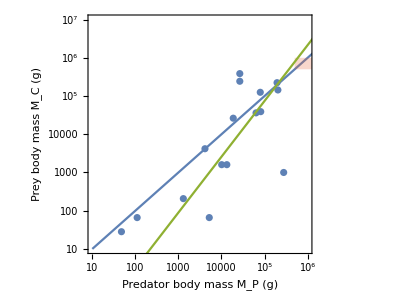

```mathematica
(*nlm = NonlinearModelFit[ExpPreymassdata*1000,nlm1*x^(nlm2),{nlm1,nlm2},x,MaxIterations->1000];
lm =LinearModelFit[Log@(ExpPreymassdata*1000),x,x];
lmparams=lm["BestFitParameters"];
nlmconfint=nlm["ParameterConfidenceIntervals",ConfidenceLevel->0.95];*)
pstyleherb=Graphics[{EdgeForm[{Black,Thickness[0.2],Opacity[0.2]}],Opacity[0.1],FaceForm[Black],Disk[]}];
PPMRPlotNLM = Show[{
ListLogLogPlot[ExpPreymassdata*1000,Frame->True,FrameLabel->{"Predator body mass M_P (g)","Prey body mass M_C (g)"},LabelStyle->Directive[FontSize->16],ImageSize->500,AspectRatio->3/4,PlotRange->{{10^1,1*10^6},{10^1,10^7}}],
ListLogLogPlot[Transpose[{Table[10^i,{i,1,7}],Table[10^i,{i,1,7}]}],Joined->True],
(*LogLogPlot[nlm[x],{x,100,5000}],*)
(*LogLogPlot[nlm[x],{x,100000,3200000},PlotStyle->Directive[Black,Thickness[0.008]]],
LogLogPlot[{nlmconfint[[1,1]]*x^(nlmconfint[[2,1]]),nlmconfint[[1,2]]*x^(nlmconfint[[2,2]])},{x,10^1,3200000},PlotStyle->Transparent,Filling->{1->{2}},FillingStyle->Directive[Green,Opacity[0.25]]],*)
(*ListLogLogPlot[predpreymassdata*1000,PlotStyle->Black],*)
(*LogLogPlot[Exp[lmparams[[1]]]*x^(lmparams[[2]]),{x,10^1,3200000},PlotStyle->ColorData[93,4]],*)
Graphics[{ColorData[97,4],Opacity[0.25],Rectangle[{Log@(5*10^5),Log@(5*10^5)},{Log@(2*10^7),Log@(1*10^6)}]}],
Graphics[Text[Style["Megatrophic range",FontSize->16,Black],{Log@(5*10^(5.5)),Log@(1*10^6)},Automatic]],
(*LogLogPlot[Exp[4]*Mp,{Mp,5,1.1*10^5},PlotStyle->ColorData[97,5]] (*Mathias general relationaship*),
LogLogPlot[Exp[3]*M,{M,5,1.1*10^5},PlotStyle->Directive[{ColorData[97,5],Dashed}]] (*Mathias felids relationaship*),*)
LogLogPlot[OptPreyMass[Mp],{Mp,10^1,10^7},Frame->True,FrameLabel->{"Prey Mass (g)","Predator Mass (g)"},LabelStyle->Directive[FontSize->16],PlotStyle->ColorData[97,3]]
},ImageSize->400,AspectRatio->3/4]
```

Calculate Intersection of Cruz/Pires relationship and Hayward relationship

Check Original Model w/o predation... do we get pretty close to the Damuth Data without predation?

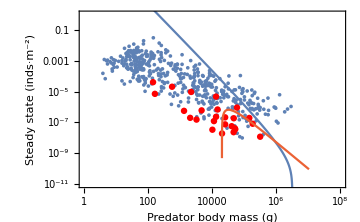

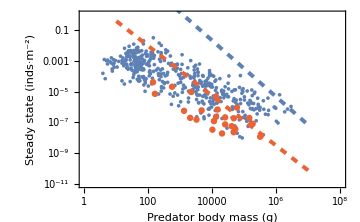

```mathematica
PercentGrowthConsumer=0.8; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidy =0.01;
PCDensityPlot=Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Predator body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/OptPreyMass[Mp])*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidy},{Mp,1,10^8},Frame->True,PlotStyle->ColorData[97,1]],
LogLogPlot[(1/Mp)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidy},{Mp,1,10^8},Frame->True,PlotStyle->ColorData[97,4]]
}]
MaxDensitiesPlot = Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Predator body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->ColorData[97,4]],
LogLogPlot[(1/OptPreyMass[Mp])*PreyDensityTheoreticalMax[OptPreyMass[Mp]]/.{w->PercentGrowthConsumer},{Mp,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/Mp)*PredatorDensityTheoreticalMax[Mp,OptPreyMass[Mp]]/.{w->PercentGrowthConsumer},{Mp,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]
}]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_densities_PC.pdf"}],PCDensityPlot]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_densities_PC.pdf

MAYBE THIS ONE WORKS PRETTY GOOD NOT BAD MEH? 
****I THINK IT WORKS 3/24/23****

```mathematica
RealQ[x_]:=(Im[x]==0)===True; 
CsolMass = ((1/OptPreyMass[Mp])*Csol)/.Mp->Mass;
PsolMass = ((1/Mp)*Psol)/.{Mp->Mass};
(*DJ=Det[JacobianFullModel];*)
DetectThresholdSol[DensitySol_,wvalue_,epsilonvalue_]:=
Module[{Sol = DensitySol},
maxexponent=8;
minexponent=1;
sollist =Table[{10^i,Sol/.{w->wvalue,Sub->epsilonvalue}/.Mass->10^i},{i,minexponent,maxexponent,0.05}];
sollistrealpos = Flatten[Position[sollist[[All,2]],_?(Re[#]>0 &&RealQ[#]&)],1];
sollistreal = sollist[[sollistrealpos]];
detminima = FindPeaks[-sollistreal[[All,2]]];
(*do any minima match the range limits?*)
massminima = sollistreal[[detminima[[All,1]],1]];
masslimitspos=Flatten[Position[massminima,_?(#==10^minexponent||#==10^maxexponent&)],1];
massminimarev=Drop[massminima,masslimitspos];
If[Length[sollistreal]==0,
exist = 0,
exist=1
];
If[Length[massminimarev]>0,
thresholdmass = massminimarev[[1]],
thresholdmass =Missing[]
];
{thresholdmass, exist}
];
```

```mathematica
{thresholdmass, exist}= DetectThresholdSol[PsolMass,0.5,0.001]
```

{50118.7,1}

```mathematica
(*wvalues = Table[i,{i,0.01,1,0.01}];
epsilonvalues = Table[10^i,{i,-3,0,0.005}];
CsolMass = ((1/OptPreyMass[Mp])*Csol)/.Mp->Mass;
PsolMass = ((1/Mp)*Psol)/.{Mp->Mass};
ThresholdsOverWEpsilonAlternate=Flatten[ParallelTable[
{thresholdsizeC,existC}= DetectThresholdSol[CsolMass,wvalues[[i]],epsilonvalues[[j]]];
{thresholdsizeP,existP} = DetectThresholdSol[PsolMass,wvalues[[i]],epsilonvalues[[j]]];
{wvalues[[i]],epsilonvalues[[j]],thresholdsizeC,thresholdsizeP, existC,existP},
{i,1,Length[wvalues]},{j,1,Length[epsilonvalues]}],1];
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsoverwepsilon2Alternate_predpersp_delonghayward.csv"}],ThresholdsOverWEpsilonAlternate,"CSV"]*)
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsoverwepsilon2Alternate_predpersp_delonghayward.csv

```mathematica
ThresholdsOverWEpsilonAlternate=Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsoverwepsilon2Alternate_predpersp_delonghayward.csv"}]];
```

```mathematica
PreyThresholdMatrixAlternate = Transpose[{ThresholdsOverWEpsilonAlternate[[All,1]],ThresholdsOverWEpsilonAlternate[[All,2]],OptPreyMass[ThresholdsOverWEpsilonAlternate[[All,3]]]}];
(*PredThresholdMatrixAlternate = Transpose[{ThresholdsOverWEpsilonAlternate[[All,1]],ThresholdsOverWEpsilonAlternate[[All,2]],ThresholdsOverWEpsilonAlternate[[All,4]]}];*)
PredThresholdMatrixAlternate = Transpose[{ThresholdsOverWEpsilonAlternate[[All,1]],ThresholdsOverWEpsilonAlternate[[All,2]],ThresholdsOverWEpsilonAlternate[[All,4]]}];

PreySizeGapPosAlternate=Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,3]],_?(#>4000&&#<25000&)],1];
PredSizeGapPosAlternate=Flatten[Position[PredThresholdMatrixAlternate[[All,3]],_?(#>4000&&#<25000&)],1];
PreyTMAlternate=PreyThresholdMatrixAlternate[[PreySizeGapPosAlternate,1;;2]];
PredTMAlternate=PredThresholdMatrixAlternate[[PredSizeGapPosAlternate,1;;2]];
MissingPosC = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,3]],_?(#==Missing[]&)],1];
MissingPointsC = Transpose[{ThresholdsOverWEpsilonAlternate[[MissingPosC]][[All,1]],ThresholdsOverWEpsilonAlternate[[MissingPosC]][[All,2]]}];
MissingPosP = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,4]],_?(#==Missing[]&)],1];
MissingPointsP = Transpose[{ThresholdsOverWEpsilonAlternate[[MissingPosP]][[All,1]],ThresholdsOverWEpsilonAlternate[[MissingPosP]][[All,2]]}];

ExtinctPosC = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,5]],_?(#==0&)],1];
ExtantPosC = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,5]],_?(#>0&)],1];
ExtinctPointsC = Transpose[{ThresholdsOverWEpsilonAlternate[[ExtinctPosC]][[All,1]],ThresholdsOverWEpsilonAlternate[[ExtinctPosC]][[All,2]]}];
ExtinctPosP = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,6]],_?(#==0&)],1];
ExtinctPointsP = Transpose[{ThresholdsOverWEpsilonAlternate[[ExtinctPosP]][[All,1]],ThresholdsOverWEpsilonAlternate[[ExtinctPosP]][[All,2]]}];
```

```mathematica
ThresholdPlotAlternate=GraphicsRow[{
Show[{
ListContourPlot[PreyThresholdMatrixAlternate,FrameLabel->{"% Growth from herbivore w","Subsidy density S (g·m^-2)"},ScalingFunctions->{None,"Log","Log"},FrameTicks->Automatic,PlotRange->{{0,1},{0.001,1},All},ContourStyle->None,ColorFunction->"StarryNightColors",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"M_C^†",LabelStyle->{Italic,FontFamily->"Times New Roman",FontSize->14},LegendMarkerSize->200],Right],ImageSize->300,LabelStyle->Directive[FontSize->16]],
(*ListLogPlot[PreyThresholdMatrix[[PreySizeGapPos,1;;2]],PlotStyle->Black],*)
Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[Transpose[{PreyTMAlternate[[All,1]],Log@PreyTMAlternate[[All,2]]}]]}],
(*Graphics[{White,Opacity[1],ConcaveHullMesh[Transpose[{MissingPointsC[[All,1]],Log@MissingPointsC[[All,2]]}],0.02,All]}],*)
Graphics[{Gray,ConcaveHullMesh[Transpose[{ExtinctPointsC[[All,1]],Log@ExtinctPointsC[[All,2]]}],0.02,All]}]
}],
Show[{
ListContourPlot[PredThresholdMatrixAlternate,FrameLabel->{"% Growth from herbivore w","Subsidy density S (g·m^-2)"},ScalingFunctions->{None,"Log","Log"},FrameTicks->Automatic,PlotRange->{{0,1},{0.001,1},All},ContourStyle->None,ColorFunction->"SiennaTones",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}},LegendLabel->"M_P^†",LabelStyle->{Italic,FontFamily->"Times New Roman",FontSize->14},LegendMarkerSize->200],Right],ImageSize->300,LabelStyle->Directive[FontSize->16]],
(*ListLogPlot[PredThresholdMatrix[[PredSizeGapPos,1;;2]],PlotStyle->Black],*)
Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[Transpose[{PredTMAlternate[[All,1]],Log@PredTMAlternate[[All,2]]}]]}]
(*,
Graphics[{White,Opacity[1],ConcaveHullMesh[Transpose[{MissingPointsP[[All,1]],Log@MissingPointsP[[All,2]]}],0.02,All]}]*)
}]
},ImageSize->850,Spacings->0]
```

-Graphics-

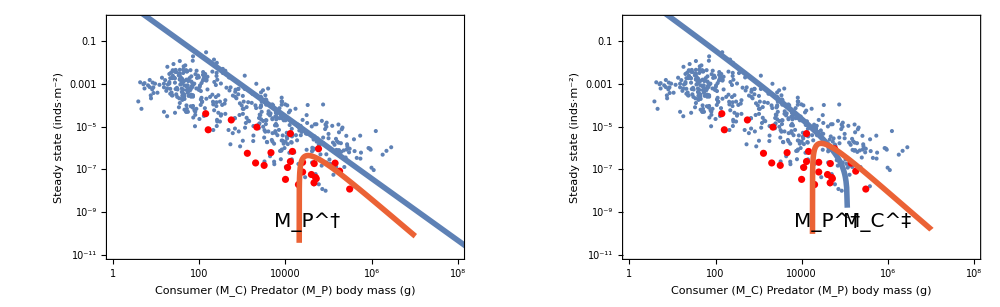

```mathematica
PercentGrowthConsumer=1; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidyValue =0.08;
ConsDensityList=Table[{10^i,((1/OptPreyMass[Mp])*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue})/.Mp->10^i},{i,1,8,0.01}];
ConsDensityListConsMass = Transpose[{OptPreyMass[ ConsDensityList[[All,1]]],ConsDensityList[[All,2]]}];
ThresholdPopulationPlotNoSub=
GraphicsRow[{
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Predator body mass M_P (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/OptPreyMass[Mp])*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
LogLogPlot[(1/Mp)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->20],{Log@(10^2.5),Log@(10^(-9))}]}](*,
Graphics[{Text["M_C^‡",{Log@(10^7),Log@(10^(-9))}]}]*)
(*ListLogLogPlot[PredDensityListPredMass,Joined->True,PlotStyle->ColorData[97,4]]*)
}],
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer (M_C) Predator (M_P) body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
(*LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],*)
ListLogLogPlot[ConsDensityListConsMass,Joined->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
LogLogPlot[(1/Mp)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->20],{Log@(10^4.5),Log@(10^(-9))}]}](*,
Graphics[{Text["M_C^‡",{Log@(10^7),Log@(10^(-9))}]}]*)
}]
},ImageSize->800];
ThresholdPopulationPlotNoSubPredSpace=
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer (M_C) Predator (M_P) body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
(*LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],*)
ListLogLogPlot[ConsDensityListConsMass,Joined->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
LogLogPlot[(1/Mp)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->20],{Log@(10^4.5),Log@(10^(-9.5))}]}](*,
Graphics[{Text["M_C^‡",{Log@(10^7),Log@(10^(-9))}]}]*)
(*LogLogPlot[(1/OptPreyMass[Mp])*PreyDensityTheoreticalMax[OptPreyMass[Mp]]/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/Mp)*PredatorDensityTheoreticalMax[Mp,OptPreyMass[Mp]]/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]*)
}];
PercentGrowthConsumer=0.5; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidyValue =0.01;
ConsDensityList=Table[{10^i,((1/OptPreyMass[Mp])*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue})/.Mp->10^i},{i,1,8,0.01}];
ConsDensityListConsMass = Transpose[{OptPreyMass[ ConsDensityList[[All,1]]],ConsDensityList[[All,2]]}];
ThresholdPopulationPlotSub=
GraphicsRow[{
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Predator body mass M_P (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/OptPreyMass[Mp])*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
LogLogPlot[(1/Mp)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->20],{Log@(10^2.5),Log@(10^(-9))}]}](*,
Graphics[{Text["M_C^‡",{Log@(10^7),Log@(10^(-9))}]}]*)
(*ListLogLogPlot[PredDensityListPredMass,Joined->True,PlotStyle->ColorData[97,4]]*)
}],
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer (M_C) Predator (M_P) body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
(*LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],*)
ListLogLogPlot[ConsDensityListConsMass,Joined->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
LogLogPlot[(1/Mp)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->20],{Log@(10^4.6),Log@(10^(-9.5))}]}](*,
Graphics[{Text["M_C^‡",{Log@(10^7),Log@(10^(-9))}]}]*)
}]
},ImageSize->800];
ThresholdPopulationPlotSubPredSpace=
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer (M_C) Predator (M_P) body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
(*LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],*)
ListLogLogPlot[ConsDensityListConsMass,Joined->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
LogLogPlot[(1/Mp)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->20],{Log@(10^4.6),Log@(10^(-9.5))}]}],
Graphics[{Text[Style["M_C^‡",FontSize->20],{Log@(10^5.75),Log@(10^(-9.5))}]}]
(*LogLogPlot[(1/OptPreyMass[Mp])*PreyDensityTheoreticalMax[OptPreyMass[Mp]]/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/Mp)*PredatorDensityTheoreticalMax[Mp,OptPreyMass[Mp]]/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]*)
}];
ThresholdPopulationPlotCombPredSpace=GraphicsRow[{ThresholdPopulationPlotNoSubPredSpace,ThresholdPopulationPlotSubPredSpace},ImageSize->1000]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdspopcomb_predpersp.pdf"}],ThresholdPopulationPlotCombPredSpace,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdspopcomb_predpersp.pdf

What is the slope of the consumer density?

```mathematica
PercentGrowthConsumer=1; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidyValue =0.01;
ConsDensityList=Table[{10^i,((1/OptPreyMass[Mp])*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue})/.Mp->10^i},{i,1,5,0.01}];
ConsDensityListConsMass = Transpose[{OptPreyMass[ ConsDensityList[[All,1]]],ConsDensityList[[All,2]]}];
CdensRealPos=Flatten[Position[Table[RealQ[Log@ConsDensityListConsMass[[i,2]]],{i,1,Length[ConsDensityListConsMass[[All,2]]]}],True],1];
Cdenslm =LinearModelFit[Log@(ConsDensityListConsMass[[CdensRealPos]]),x,x];
lmparams=Cdenslm["BestFitParameters"]
```

{2.94783,-1.45115}